# Notebook for : Structure formation and quasi spherical collapse from initial curvature perturbations with numerical relativity simulations by Munoz and Bruni

Geoff Cope
University of Utah
                                                                                                             𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
February 20, 2023

```mathematica
(* PLEASE NOTE:  NONE OF THE PLOTS INCLUDED HERE CORRESPOND TO ANYTHING IN THE PAPER.  THEIR PURPOSE IS SIMPLY TO REMIND ONE WHAT KIND OF PLOTS DO WHAT AND HOW TO FIND VARIOUS OPTIONS FOR PLOTTING - FIX THIS LATER *)
```

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

```mathematica
Hyperlink["Spin Weighted Spheroidal Harmonics",
"https://bhptoolkit.org/SpinWeightedSpheroidalHarmonics/"]
```

[Spin Weighted Spheroidal Harmonics](https://bhptoolkit.org/SpinWeightedSpheroidalHarmonics/)

## Hyperlink To Article

```mathematica
Hyperlink["Effect of GREA on the Gravitation Collapse of Neutron Stars by Garcia Bellido",
"https://arxiv.org/abs/2302.09033"]
```

[Effect of GREA on the Gravitation Collapse of Neutron Stars by Garcia Bellido](https://arxiv.org/abs/2302.08537)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 39 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,NaturalLanguageProcessingLoader`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

```mathematica
Needs["VariationalMethods`"]
```

## Custom Notation

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[p]-> dp , 
Dt[q]-> dq , 
Dt[r]-> dr , 
Dt[t]-> dt , 
Dt[u]-> du , 
 Dt[v]-> dv , 
 Dt[w]-> dw , 
Dt[x]-> dx , 
Dt[y]-> dy , 
Dt[z]-> dz ,
Dt[𝓇] -> d𝓇 , 
Dt[𝓉] -> d𝓉  , 
Dt[𝓅] -> d𝓅 , 
Dt[𝓆]-> d𝓆 ,
Dt[ψ]-> dψ ,    
 Dt[θ] -> dθ , 
Dt[ϕ] -> dϕ  ,
Dt[η] -> dη  , 
Dt[χ]-> dχ , 
Dt[ρ] -> dρ ,
Dt[φ] -> dφ , 
 Dt[𝓉] -> d𝓉 , 
Dt[𝓍]-> d𝓍 , 
Dt[𝓎]-> d𝓎 , 
Dt[𝓏] -> d𝓏,
Dt[T]-> dT , 
Dt[U]-> dU , 
Dt[V]-> dV ,
Dt[X]-> dX , 
Dt[Y]-> dY , 
Dt[Z]-> dZ , 
Dt[𝓇]-> d𝓇  , 
Dt[Φ]-> dΦ 
};
dtReplace // TableForm
```

Dt[p]→dp
Dt[q]→dq
Dt[r]→dr
Dt[t]→dt
Dt[u]→du
Dt[v]→dv
Dt[w]→dw
Dt[x]→dx
Dt[y]→dy
Dt[z]→dz
Dt[𝓇]→d𝓇
Dt[𝓉]→d𝓉
Dt[𝓅]→d𝓅
Dt[𝓆]→d𝓆
Dt[ψ]→dψ
Dt[θ]→dθ
Dt[ϕ]→dϕ
Dt[η]→dη
Dt[χ]→dχ
Dt[ρ]→dρ
Dt[φ]→dφ
Dt[𝓉]→d𝓉
Dt[𝓍]→d𝓍
Dt[𝓎]→d𝓎
Dt[𝓏]→d𝓏
Dt[T]→dT
Dt[U]→dU
Dt[V]→dV
Dt[X]→dX
Dt[Y]→dY
Dt[Z]→dZ
Dt[𝓇]→d𝓇
Dt[Φ]→dΦ

```mathematica
M /: Dt[M] = 0 ;  (* Mass of Schwarzschild is constant *) (* We use M for mass and m for null vector *)
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## ContourPlot3D

```mathematica
?ContourPlot3D
```

```mathematica
Clear[figure1]
figure1 = 
ContourPlot3D[Sin[2 π x]+Sin[2 π y]+Sin[2 π z] , {x,-π/2,π/2} , {y,-π/2,π/2},{z,-π/2,π/2}]
```

## SliceContourPlot3D

```mathematica
?SliceContourPlot3D
```

```mathematica
Clear[figure10]
figure10 = 
SliceContourPlot3D[Sin[2 π x]+Sin[2 π y]+Sin[2 π z],"CenterPlanes", {x,-π/2,π/2} , {y,-π/2,π/2},{z,-π/2,π/2}]
```

## SliceDensityPlot3D

```mathematica
?SliceDensityPlot3D
```

```mathematica
Clear[figure10a]
figure10a = 
SliceDensityPlot3D[Sin[2 π x]+Sin[2 π y]+Sin[2 π z],"CenterPlanes", {x,-π/2,π/2} , {y,-π/2,π/2},{z,-π/2,π/2}]
```

## DensityPlot3D

```mathematica
?DensityPlot3D
```

```mathematica
DensityPlot3D[Sin[2 π x]+Sin[2 π y]+Sin[2 π z], {x,-π/2,π/2} , {y,-π/2,π/2},{z,-π/2,π/2},ColorFunction->"SunsetColors",PlotLegends->Automatic]
```

## VectorPlot3D

```mathematica
?VectorPlot3D
```

```mathematica
VectorPlot3D[Evaluate[Grad[Sin[2 π x]+Sin[2 π y]+Sin[2 π z],{x,y,z}]],{x,-π/2,π/2} , {y,-π/2,π/2},{z,-π/2,π/2}]
```

## StreamPlot3D

```mathematica
?StreamPlot3D
```

```mathematica
StreamPlot3D[Grad[Sin[2 π x]+Sin[2 π y]+Sin[2 π z],{x,y,z}], {x,-π/2,π/2} , {y,-π/2,π/2},{z,-π/2,π/2}]
```

-Graphics3D-

## SliceVectorPlot3D

```mathematica
?SliceVectorPlot3D
```

```mathematica
SliceVectorPlot3D[Grad[Sin[2 π x]+Sin[2 π y]+Sin[2 π z],{x,y,z}], "CenterPlanes",{x,-π/2,π/2} , {y,-π/2,π/2},{z,-π/2,π/2}]
```

-Graphics3D-

## RegionPlot3D

```mathematica
?RegionPlot3D
```

```mathematica
RegionPlot3D[ Sin[2 π x]+Sin[2 π y]+Sin[2 π z]> 9/10,  {x,-π/2,π/2} , {y,-π/2,π/2},{z,-π/2,π/2}]
```

-Graphics3D-

## AmbientLight (Animation)

```mathematica
?AmbientLight
```

```mathematica
col={Red,Green,Blue};
objs=Graphics3D[{Specularity[White,2],EdgeForm[],Cylinder[{{2,2,0},{2,2,4}}],Cylinder[{{6,2,0},{6,2,4}}],Cylinder[{{10,2,0},{10,2,4}}]}];
walls=ParametricPlot3D[{{u,v-2,0},{u,4,2v}},{u,-2,14},{v,0,6},PlotPoints->15,MaxRecursion->0,PlotStyle->Specularity[White,2],Mesh->None,Axes->False];
srcs[pos_]:=Graphics3D[MapThread[{DirectionalLight[#1,{{0,-1,0},{0,0,0}}],Sphere[{#2,0,8},.3]}&,{col,pos}]];
lights[pos_]:=Join[{AmbientLight[GrayLevel[.1]]},Sequence@@MapThread[{SpotLight[#1,{{#2,0,8},{#2,3,0}},{Pi/2,20}],{PointLight[#1,{#2,0,8},{0,8,0}]}}&,{col,pos}]];
```

```mathematica
Animate[With[{rx=-6Cos[t]+6,gx=6Sin[t]+6,bx=6Cos[t]+6},Show[objs,walls,srcs[{rx,gx,bx}],Lighting->lights[{rx,gx,bx}],Background->Black,Boxed->False,ImageSize->300]],{t,0,2Pi},SaveDefinitions->True,AnimationRunning->False]
```

## Directional Light (Animation)

```mathematica
?DirectionalLight
```

```mathematica
col={Red,Green,Blue};
objs=Graphics3D[{Specularity[White,2],EdgeForm[],Cylinder[{{2,2,0},{2,2,4}}],Cylinder[{{6,2,0},{6,2,4}}],Cylinder[{{10,2,0},{10,2,4}}]}];
walls=ParametricPlot3D[{{u,v-2,0},{u,4,2v}},{u,-2,14},{v,0,6},PlotPoints->15,MaxRecursion->0,PlotStyle->Specularity[White,2],Mesh->None,Axes->False];
srcs[pos_]:=Graphics3D[MapThread[{DirectionalLight[#1,{{0,-1,0},{0,0,0}}],Sphere[{#2,0,8},.3]}&,{col,pos}]];
lights[pos_]:=Join[{AmbientLight[GrayLevel[.1]]},Sequence@@MapThread[{SpotLight[#1,{{#2,0,8},{#2,3,0}},{Pi/2,20}],{PointLight[#1,{#2,0,8},{0,8,0}]}}&,{col,pos}]];
```

```mathematica
Animate[With[{rx=-6Cos[t]+6,gx=6Sin[t]+6,bx=6Cos[t]+6},Show[objs,walls,srcs[{rx,gx,bx}],Lighting->lights[{rx,gx,bx}],Background->Black,Boxed->False,ImageSize->300]],{t,0,2Pi},SaveDefinitions->True,AnimationRunning->False]
```

## PointLight (Animation)

```mathematica
?PointLight
```

```mathematica
p1[θ_]:=RotationTransform[θ,{0,0,1}][{0,2,0}];
p2[θ_]:=RotationTransform[θ+Pi/2,{1,0,1}][{0,2,0}];
p3[θ_]:=RotationTransform[θ+Pi,{1,0,0}][{0,2,0}];
p4[θ_]:=RotationTransform[θ+3Pi/2,{1,0,-1}][{0,2,0}];
```

```mathematica
Animate[Graphics3D[{AmbientLight[GrayLevel[.1]],PointLight[Red,p1[θ]],PointLight[Green,p2[θ]],PointLight[Blue,p3[θ]],PointLight[Yellow,p4[θ]],Specularity[White,30],Sphere[],Sphere[p1[θ],.4],Sphere[p2[θ],.4],Sphere[p3[θ],.4],Sphere[p4[θ],.4]},Lighting->None,PlotRange->2.5,Background->Black,Boxed->False,ImageSize->300],{θ,0,2Pi},SaveDefinitions->True, AnimationRunning->False]
```

## SpotLight (Animation)

```mathematica
?SpotLight
```

```mathematica
obj=RevolutionPlot3D[{8+Cos[t],2Sin[t]},{t,0,2Pi},Mesh->None,PlotStyle->Directive[White,Specularity[White,50]],Axes->False,Boxed->False];
```

```mathematica
Grid[Table[obj/.Rule[Lighting,spec_]:>Rule[Lighting,(SpotLight[ColorData["SouthwestColors"][RandomReal[]],Scaled[#],{Pi/4,100}]&)/@RandomReal[{-4,4},{5,3}]],{3},{3}]]
```

## RGBColor

```mathematica
?RGBColor
```

```mathematica
Graphics3D[{Opacity[.7],{RGBColor[#],Cuboid[#,#+.1]}&/@Tuples[Range[0,1,.2],3]},Axes->True,AxesLabel->{"Red","Green","Blue"},Lighting->"Neutral"]
```

## Specularity

```mathematica
?Specularity
```

```mathematica
Table[Graphics3D[{Orange,Specularity[White,n],Sphere[]}],{n,{5,20,100}}]
```

```mathematica
Table[Graphics3D[{Black,Specularity[c,10],Sphere[]},Lighting->"Neutral"],{c,{Red,Green,Blue}}]
```

## Glow

```mathematica
?Glow
```

```mathematica
Plot3D[Abs[Zeta[σ+ⅈ ω]],{σ,-2,2},{ω,0,40},ColorFunction->Function[{σ,ω,z},Glow[Hue[Rescale[Arg[Zeta[σ+ⅈ ω]],{-Pi,Pi},{0,1}]]]],
ColorFunctionScaling->False]//Quiet
```

## Color Function

```mathematica
?ColorFunction
```

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},ColorFunction->"BlueGreenYellow"]
```

-Graphics3D-

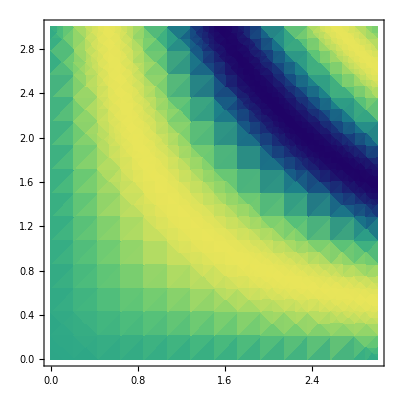

```mathematica
DensityPlot[Sin[x y],{x,0,3},{y,0,3},ColorFunction->"BlueGreenYellow"]
```

## NormalsFunction

```mathematica
?NormalsFunction
```

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2},NormalsFunction->Automatic,Mesh->None]
```

-Graphics3D-